# Difference between Time and Space Expectations

There is a divorce in two expectations if there is non-ergodicity.
The non-ergodicity has massive consequences.
Every trader says take all the risk you want.
But make sure you are never absorbed.
You should say no to a 1000 things.
Says no all the time due to absorption.
You can take a lot of risk just by avoiding.

## Weak Non-Ergodicity

Stochastic process.
Independent increment.
Only when you average across all sample paths, then you get 0. Not one sample path.
The martingale property is the following.
The expectation is the expectation at the last price.
It is not ergodic, since time average does not give you 0. 
The law of large number works in space.
Your returns will be ergodic if there is no drift.

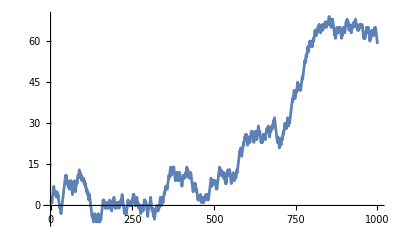

```mathematica
Clear[gen]; gen[μ1_,μ2_,n_]:=ta=Table[tr=RandomVariate[BernoulliDistribution[0.5]]; If[tr==1,μ1,-μ2],{n}]
gen[1,1,1000]; Clear[S]; S[0]=1; (* 1000 steps *)
S=Table[S[t]=(S[t-1] + ta[[t]]),{t,1,Length[ta]}];
S = Table[S[[i]],{i,1,1000}];
S//ListLinePlot
```

## Strong Non-Ergodicity

Introduce an absorbing barrier at 80. 
In 2D, you will be absorbed.
A drunk man will find his way home.
A drunk bird will lost forever. (Kakutani)
The recurrence theorem does not apply in dimension 3 AND above.

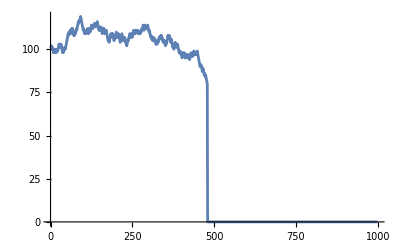

```mathematica
Clear[gen]; gen[μ1_,μ2_,n_]:=ta=Table[tr=RandomVariate[BernoulliDistribution[0.5]]; If[tr==1,μ1,-μ2],{n}]
gen[1,1,1000]; Clear[S]; S[0]=100;
S=Table[S[t]=(S[t-1] + ta[[t]]),{t,1,Length[ta]}];
X[L_]:= Table[If[i>=(Position[S,Select[S,# < L &][[1]]]//Min),0,S[[i]]],{i,2,1000}]; X[80]//ListLinePlot (* Absorbing barrier there *)
```